```mathematica
SetDirectory["/Users/George/Documents/"]; (*Change to your directory, if needed *)
```

```mathematica
kmin=10^(-3);
kmax=20;
```

```mathematica
Clear[rval]
```

```mathematica
rval=1;
xval=0.1;
amin=0.002;
amax=1;
```

```mathematica
(*Change to desired background cosmology*)
```

```mathematica
Om=0.281; (*For Wmap9 *)
```

```mathematica
(*Om=0.3089(*For Planck *)
```

```mathematica
adot=Sqrt[Om /a+(1-Om)a*a];
```

```mathematica
intToday=Assuming[ Int∈Reals ,Integrate[1/(adot^3),{a,0,amin}]];
```

```mathematica
H=adot/a;
```

```mathematica
Clear[H1]
```

```mathematica
H1=(H)/.a->amin
```

5926.63

```mathematica
Clear[D1]
```

```mathematica
D1=2.5 Om H1 intToday;
```

```mathematica
H0=H/.a->amax;
```

```mathematica
Clear[DH1]
```

```mathematica
DH1=D[(H),a];
```

```mathematica
DH1=DH1/.a->amin;
```

```mathematica
Clear[adotpast]
```

```mathematica
adotpast=adot/.a->amin;
```

```mathematica
Clear[der]
```

```mathematica
der=2.5 Om (DH1*intToday+H1/(adotpast^3));
```

```mathematica
(*Hu-Sawicki parameters *)
```

```mathematica
n=1;
```

```mathematica
c=2997;
```

```mathematica
fr0=10^-5;
```

```mathematica
(*Defining mass terms in f(R) *)
```

```mathematica
Clear[m]
```

```mathematica
m[a_]=(1/c)Sqrt[1/(2fr0)]Sqrt[(Om+4 (1-Om))^(-n-1)] Sqrt[(Om/(a^3)+4 (1-Om))^(2+n)];
```

```mathematica
Clear[M2]
```

```mathematica
M2[a_]=(9/4)(1/c/c/c/c)(1/(fr0^2))(Om+4 (1-Om))^(-4) (Om/(a^3)+4 (1-Om))^(5)
```

2.80761×10^-6 (2.876+0.281/a^3)^5

```mathematica
Clear[M3]
```

```mathematica
M3[a_]=(45/8)(1/c/c/c/c/c/c)(1/(fr0^3))(Om+4 (1-Om))^(-6) (Om/(a^3)+4 (1-Om))^(7)
```

7.8407×10^-9 (2.876+0.281/a^3)^7

```mathematica
(*m=Sqrt[1-(0.5/a)^3]*)
```

```mathematica
Ddot=D[adot,a];
```

```mathematica
Clear[s]
```

```mathematica
s=NDSolve[{(adot^2)* y''[a]+(adot*Ddot+2 adot H) y'[a]==(1.5*(Om/(Om+(1-Om) a^3)))(adot/a)^2  y[a],y'[amin]==der,y[amin]==D1},y,{a,amin,amax},AccuracyGoal->13,PrecisionGoal->20];
```

```mathematica
Clear[lot]
```

```mathematica
lot=D[Evaluate[y[a]/.First@s],a];
```

```mathematica
valtoday = Evaluate[y[a]/.First@s]/.a->amax//N;
```

```mathematica
Clear[geff]
```

```mathematica
geff[k_,a_]=k^2/(k^2+( a m[a])^2)/3;
```

```mathematica
Clear[Eqn]
```

```mathematica
Eqn[k_,a_]= D[p[a],a,a]+(adot*Ddot+2 (adot^2)/a)D[p[a],a]/(adot^2)==(1.5*Om /(a^3))  p[a](1+geff[k,a])/(adot^2);
```

```mathematica
Clear[del]
```

```mathematica
del[a_]:=Evaluate[y[a]/.First@s]
```

```mathematica
Clear[jk]
```

```mathematica
jk[a_]=D[del[a],a];
```

```mathematica
Clear[nsol1]
```

```mathematica
Clear[dgrowth]
```

```mathematica
(*growing mode *)
```

```mathematica
Clear[dgrowth]
```

```mathematica
tf[k_?NumericQ]:=First[p[a]/.NDSolve[{Eqn[k,a],p[amin]==del[amin],Derivative[1][p][amin]==jk[amin]},p[a],{a,amin,amax},Method->"ExplicitRungeKutta"]]
```

```mathematica
Clear[dgrowth]
```

```mathematica
dgrowth[k_,anew_]:=tf[k]/.a->anew
```

```mathematica
dergrowth[k_,anew_]:=D[tf[k],a]/.a->anew
```

```mathematica
Plot3D[(dgrowth[k,anew])/del[1],{anew,0.01,1},{k,0.001,1}]
```

-Graphics3D-

```mathematica
(*decaying mode soln *)
decmod[a_] = (adot/a);
```

```mathematica
Clear[Ppi]
```

```mathematica
Afact[k_,a_]=((1.5*Om /(a^3)))(1+geff[k,a]);
```

```mathematica
K2fl[k_,r_,x_,a_]=2(Afact[k r, a]+Afact[k Sqrt[1+r^2-2r x], a]-2 Afact[0, a]) (x^2+r^2-2r x)/(1+r^2-2r x)+(Afact[k r, a]- Afact[0, a]) (r x-r^2)/(r^2)+(Afact[k Sqrt[1+r^2-2r x], a]- Afact[0, a]) (r x-r^2)/(1+r^2-2r x);
```

```mathematica
Ppi[k_,a_]=(k^2+(a m[a] )^2)/a^2
```

(0.000558531 (2.876+0.281/a^3)^3 a^2+k^2)/a^2

```mathematica
Clear[Source]
```

```mathematica
(*Source factor for [p,k-p] configuration *)
```

```mathematica
Source[k_,r_,x_,a_]=Afact[k,a]dgrowth[k r,a]dgrowth[k Sqrt[1+r^2-2r x], a]-((x^2+r^2-2r x)/(1+r^2-2r x))(Afact[k r,a]+Afact[k Sqrt[1+r^2-2r x],a]-Afact[k,a])dgrowth[k r,a]dgrowth[k Sqrt[1+r^2-2r x], a]-(2 Afact[0, a] k/(3 a))^2 M2[a] dgrowth[k r,a]dgrowth[k Sqrt[1+r^2-2r x], a]/(6 Ppi[k,a] Ppi[k r,a] Ppi[k Sqrt[1+r^2-2r x], a])+  (m[a]^2/Ppi[k,a])K2fl[k,r,x,a] dgrowth[k r,a]dgrowth[k Sqrt[1+r^2-2r x], a];
```

```mathematica
(*Solve for 2nd order ΛCDM growth factor, in case needed*)
```

```mathematica
dsecond[a_]:=-(3/7) (Om/(Om+(1-Om) a^3))^(-1/143)(del[a]/valtoday)^2
```

```mathematica
Plot[dsecond[a],{a,amin,amax}];
```

```mathematica
bound[a_]:=-(3/7)(Om/(Om+(1-Om) a^3))^(-1/143)(del[a])^2
```

```mathematica
derop2[a_]=D[bound[a],a];
```

```mathematica
s2=NDSolve[{(adot^2)* yy''[a]+(adot*Ddot+2 adot H) yy'[a]==(1.5*Om /(a^3))  (yy[a]-(del[a] )^2),yy[amin]==bound[amin],yy'[amin]==derop2[amin]},yy,{a,amin,amax}];
```

```mathematica
dgrowth2=Evaluate[yy[a]/.First@s2]
```

InterpolatingFunction[…][a]

```mathematica
secondgr[a_]=dgrowth2
```

InterpolatingFunction[…][a]

```mathematica
Clear[Dsecondgr]
```

```mathematica
Dsecondgr[a_]=D[secondgr[a],a]
```

InterpolatingFunction[…][a]

```mathematica
(*Differential equation that gives D(2)[p,k-p]*)
```

```mathematica
Clear[Eqn2]
```

```mathematica
Eqn2[k_,r_,x_,a_]= D[pk[a],a,a]+(adot*Ddot+2 (adot^2)/a)D[pk[a],a]/(adot^2)==(Afact[k,a]pk[a]+ Source[k,r,x,a])/(adot^2);
```

```mathematica
(*Eqn2= D[pk[k,a],a,a]+(adot*Ddot+2 adot H)D[pk[k,a],a]/(adot^2)==(Afact[k,a]pk[k,a]+(Afact[k,a]dgrowth[k ,a]dgrowth[k , a]))/(adot^2);
```

```mathematica
Clear[nsolsecond]
```

```mathematica
nsolsecond[k_?NumericQ,r_,x_]:=First[pk[a]/.NDSolve[{Eqn2[k,r,x,a],pk[amin]==- secondgr[amin](1-(x^2+r^2-2r x)/(1+r^2-2r x)),Derivative[1][pk][amin]==- Dsecondgr[amin](1-(x^2+r^2-2r x)/(1+r^2-2r x)) },pk[a],{a,amin,amax},PrecisionGoal->20,AccuracyGoal->13]]
```

```mathematica
Clear[D2growth]
```

```mathematica
D2growth[k_,r_,x_,anew_]:=nsolsecond[k,r,x]/.a->anew
```

```mathematica
(*K2fl factor for [p,k] configuration *)
```

```mathematica
Clear[K2flpk]
```

```mathematica
K2flpk[k_,r_,x_,a_]=2(Afact[k r, a]+Afact[k , a]-2 Afact[0, a])  (x^2)+(Afact[k r, a]- Afact[0, a]) (x)/(r)+(Afact[k, a]- Afact[0, a]) (r x);
```

```mathematica
(*Source factor for [p,k] configuration *)
```

```mathematica
Clear[Sourcepk]
```

```mathematica
Sourcepk[k_,r_,x_,a_]=Afact[k Sqrt[1+r^2+2r x], a]dgrowth[k r,a]dgrowth[k ,a]-(x^2)(Afact[k r,a]+Afact[k,a]-Afact[k Sqrt[1+r^2+2r x],a])dgrowth[k r,a]dgrowth[k , a]-(2 Afact[0, a] k Sqrt[1+r^2+2r x]/(3 a))^2 M2[a] dgrowth[k r,a]dgrowth[k , a]/(6 Ppi[k,a] Ppi[k r,a] Ppi[k Sqrt[1+r^2+2r x], a])+ (m[a]^2/Ppi[k Sqrt[1+r^2+2r x],a])K2flpk[k,r,x,a] dgrowth[k r,a]dgrowth[k , a];
```

```mathematica
(*Differential equation that gives D(2)[p,k]*)
```

```mathematica
Clear[Eqndif2]
```

```mathematica
Eqndif2[k_,r_,x_,a_]= D[pkdif[ a],a,a]+(adot*Ddot+2 (adot^2)/a)D[pkdif[ a],a]/(adot^2)==((Afact[ Sqrt[1+r^2+2r x] k,a]pkdif[ a])+ Sourcepk[k,r,x,a])/(adot^2);
```

```mathematica
Clear[nsolseconddif]
```

```mathematica
nsolseconddif[k_?NumericQ,r_,x_]:=First[pkdif[a]/.NDSolve[{Eqndif2[k,r,x,a],pkdif[amin]==-secondgr[amin](1-x^2),Derivative[1][pkdif][amin]==-Dsecondgr[amin](1-x^2)},pkdif[a],{a,amin,amax},PrecisionGoal->20,AccuracyGoal->13]]
```

```mathematica
(* D(2)[p,k]*)
```

```mathematica
Clear[D2pk]
```

```mathematica
D2pk[k_,r_,x_,anew_]:=nsolseconddif[k,r,x]/.a->anew
```

```mathematica
Clear[der2pk]
```

```mathematica
der2pk[k_,r_,x_,anew_]:=D[nsolseconddif[k,r,x],a]/.a->anew
```

```mathematica
derder2pk[k_,r_,x_,anew_]:=D[nsolseconddif[k,r,x],a,a]/.a->anew
```

```mathematica
(*D2φ factor for [p,k] configuration *)
```

```mathematica
Clear[D2phi]
```

```mathematica
D2phi[k_,r_,x_,a_]:=D2pk[k,r,x,a] +(1+x^2) dgrowth[Abs[k r],a] dgrowth[k ,a]-(2 Afact[0, a]/3) (M2[a]+2 3(3/(2Afact[0, a] ))^2 K2flpk[k,r,x,a] Ppi[k ,a] Ppi[k r,a])/(3 Ppi[k ,a] Ppi[k r,a]) dgrowth[Abs[k r],a] dgrowth[k ,a];
```

```mathematica
Clear[K3rd]
```

```mathematica
(*K(3)_δI screening factor that will be used for source term below*)
K3rd[k_,r_,x_,a_]:=
(1/6) ( (2 Afact[0,a]/3)^2 6 M2[a]/(Ppi[k,a]Ppi[0,a])+ (2 Afact[0,a]/3)^3 (M3[a]/(Ppi[k,a] Ppi[k r,a]^2)-  M2[a] (M2[a]+12(Afact[k r,a]-Afact[0,a])(3/(2 Afact[0,a]))^2Ppi[k r,a] Ppi[k r,a])/(Ppi[0,a] Ppi[k,a] Ppi[k r,a]^2)))+(1/3) ((2 Afact[0,a]/3)^2 3 M2[a] (1+x^2+D2pk[k,r,x,a]/(dgrowth[k,a] dgrowth[Abs[k r],a]))/(Ppi[k r,a]Ppi[k Sqrt[1+r^2+2r x],a])+ (2 Afact[0,a]/3)^3  (M3[a]/(Ppi[k,a] Ppi[k r,a]^2)-M2[a] (M2[a] +6 (3/(2 Afact[0,a]))^2 (2 x^2 (Afact[k,a]+Afact[k r,a]-2 Afact[0,a])+r x (Afact[k,a]-Afact[0,a])+(x/r)(Afact[k r,a]-Afact[0,a]))Ppi[k,a] Ppi[k r,a])/(Ppi[k Sqrt[1+r^2+2r x],a] Ppi[k,a] Ppi[k r,a]^2)));
```

```mathematica
(*Source factor for D(3)[k,-p,p] differential equation *)
```

```mathematica
Clear[Source3rd]
```

```mathematica
Source3rd[k_,r_,x_,a_]:=dgrowth[Abs[k r],a]((Afact[k r,a]-Afact[k ,a])D2pk[k,r,x,a]+adot^2 derder2pk[k,r,x,a]+(adot*Ddot+2 (adot^2)/a)der2pk[k,r,x,a] ) (1-x^2)/(1+r^2+2r x)-dgrowth[Abs[k r],a] (Afact[k r,a]+Afact[k Sqrt[1+r^2+2r x],a]-2 Afact[k ,a])D2pk[k,r,x,a]+(2 Afact[k ,a]- Afact[k r,a]-Afact[k Sqrt[1+r^2+2r x],a])(dgrowth[Abs[k r],a])^2 dgrowth[k ,a] x^2 -(Afact[k Sqrt[1+r^2+2r x],a]-Afact[k ,a])(dgrowth[Abs[k r],a])^2 dgrowth[k ,a] -(m[a]^2/Ppi[k Sqrt[1+r^2+2r x],a] K2flpk[k,r,x,a]-(2 Afact[0, a] k Sqrt[1+r^2+2r x]/(3 a))^2M2[a]/(6 Ppi[k ,a] Ppi[k r,a] Ppi[k Sqrt[1+r^2+2r x], a]))(dgrowth[Abs[k r],a])^2 dgrowth[k ,a]+m[a]^2/Ppi[k ,a]((2(x^2+r^2+2r x)/(1+r^2+2r x)-(x+r)/r)(Afact[k r,a]-Afact[0, a])D2pk[k,r,x,a] dgrowth[Abs[k r],a]+(2(x^2+r^2+2r x)/(1+r^2+2r x)-(r x+r^2)/(1+r^2+2r x))(Afact[k Sqrt[1+r^2+2r x],a]-Afact[0, a])D2phi[k ,r,x,a] dgrowth[Abs[k r],a]+3 x^2 (Afact[k r,a]+Afact[k ,a]-2 Afact[0, a])(dgrowth[Abs[k r],a])^2 dgrowth[k ,a] )- 0.5(k^2/a^2)/(6 Ppi[k,a]) K3rd[k,r,x,a] dgrowth[k,a] dgrowth[Abs[k r],a]^2 ;
```

```mathematica
Clear[Source3rdsym]
```

```mathematica
Source3rdsym[k_,r_,x_,a_]:= (Source3rd[k,r,x,a]+Source3rd[k,-r,x,a]);
```

```mathematica
Clear[Eqn3d]
```

```mathematica
Eqn3d[k_,r_,x_,a_]:= D[pk3d[a],a,a]+(adot*Ddot+2 (adot^2)/a)D[pk3d[a],a]/(adot^2)==(Afact[k,a]pk3d[a]+ Source3rdsym[k,r,x,a])/(adot^2);
```

```mathematica
D3LCDM[a_]=(5/7)(del[a])^3;
```

```mathematica
Der3LCDM[a_]=D[D3LCDM[a],a];
```

```mathematica
Clear[nsol3d]
```

```mathematica
nsol3d[k_?NumericQ,r_,x_]:=First[pk3d[a]/.NDSolve[{Eqn3d[k,r,x,a],pk3d[amin]==(2/3)D3LCDM[amin] (1-x^2)^2/(1+r^2-2 r x),Derivative[1][pk3d][amin]==(2/3)Der3LCDM[amin] (1-x^2)^2/(1+r^2-2 r x) },pk3d[a],{a,amin,amax},PrecisionGoal->20,AccuracyGoal->13]]
```

```mathematica
Clear[D3symgrowth]
```

```mathematica
D3symgrowth[k_,r_,x_,anew_]:=nsol3d[k,r,x]/.a->anew
```

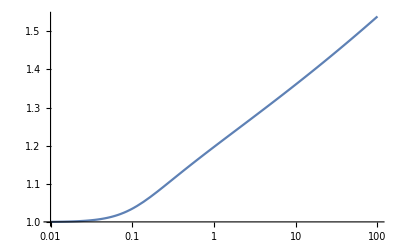

```mathematica
(*The code has now calculated the 1st, 2nd and 3rd order growth factors that are needed for calculating the CLPT statistics in f(R) MG gravity. As explained in the paper, the 1st order growth factor for MG is a function k and time a. Here it is given by the function dgrowth[k,a]. The 2nd and 3rd order growth factors are functions of k, r, x and a and are given by D2pk[k,r,x,a], D2growth[k,r,x,a] and D3symgrowth[k,r,x,a].
D2pk and D2growth are the 2 different configurations, D2(p,k) and D2(p,k-p]) that we need for CLPT.
Plotting all of these below vs k, for r=0.9, x=0.05 and a=1. del[a] is the LCDM linear growth factor. *)
LogLinearPlot[dgrowth[k,1]/del[1],{k,0.01, 100}]
```

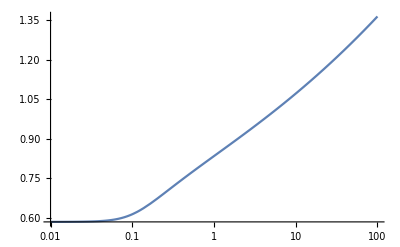

```mathematica
LogLinearPlot[(7/3)D2growth[k,0.9,0.05,1]/(del[1] del[1]),{k,0.01, 100}]
```

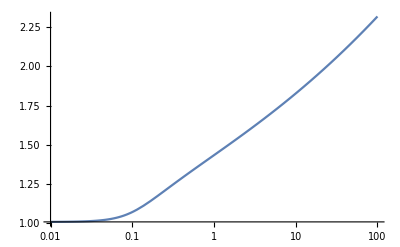

```mathematica
LogLinearPlot[(7/3)D2pk[k,0.9,0.05,1]/(del[1] del[1]),{k,0.01, 100}]
```

```mathematica
(*LogLinearPlot[(21/10)D3symgrowth[k,0.9,0.05,1]/(del[1] del[1]del[1]),{k,0.01, 100}]
```

```mathematica
(*End of growth factor calculation section *)
```

```mathematica
(*This commented out part can be used to store tabulated values of the various growth factors for values of k, r, x, that will be used in the Python module. It can also be used to produce and store linear MG power spectra, given a LCDM power spectrum for the desired background cosmology. *)
```

```mathematica
(*zref=1.0014329681653127
```

```mathematica
(*zref=0.4986379636906084*)
```

```mathematica
(*aref=1./(1+zref)
```

```mathematica
(*logspace[a_,b_,n_]:=Exp[Range[a,b,(b-a)/(n-1)]]
```

```mathematica
(*Clear[dk]
```

```mathematica
(*dk=(1.0-0.001)/9
```

```mathematica
(*Clear[dr]
```

```mathematica
(*dr=(0.9-0.001)/29
```

```mathematica
(*Clear[dx]
```

```mathematica
(*dx=(1+1)/8//N
```

```mathematica
(*krange=logspace[Log[10^(-3)], Log[10^2], 80]//N
```

```mathematica
(*rrange=logspace[Log[10^(-3)], Log[10^2], 80]//N
```

```mathematica
(*Table[x,{x,-1,1,dx}]
```

```mathematica
(*Table[krange[[i]],{i,1,80,1}]
```

```mathematica
(*Table[rrange[[j]],{j,1,80,1}]
```

```mathematica
(*Clear[testtabble]
```

```mathematica
(*testtabble=ParallelTable[{D3symgrowth[krange[[i]],rrange[[j]],x,aref]},{i,1,80,1},{j,1,80,1},{x,-1,1,dx}];
```

```mathematica
(*Export["D3symgrowthFr5z1planckp80809.txt", Flatten[testtabble], "Table"];
```

```mathematica
(*FilePrint["D3symgrowthFr4p80809new.txt"];
```

```mathematica
(*Clear[testtabble]
```

```mathematica
(*krangegrowth=logspace[Log[10^(-6)], Log[10^5], 3000]//N;
```

```mathematica
(*testtabble=ParallelTable[{dgrowth[krangegrowth[[i]],aref]},{i,1,3000,1}];
```

```mathematica
(*Export["D1growthFr5z1planckp2000.txt", Flatten[testtabble], "Table"];
```

```mathematica
(*FilePrint["D1growthFr4z0p2000.txt"]
```

```mathematica
(*Clear[datapow]
```

```mathematica
(*datapow=Import["plin_wmap9.txt",{"Data",All}];
```

```mathematica
(*Plin[k_]=Interpolation[datapow][k]
```

```mathematica
(*Clear[datapow9]
```

```mathematica
(*datapow9=Import["Camb_new_wmap9.txt",{"Data",All}];*)
(*datapow9=Import["plin_planck.txt",{"Data",All}];
```

```mathematica
(*Plinwamp9[k_]:=Interpolation[datapow9][k]
```

```mathematica
(*Clear[PlinMG]
```

```mathematica
(*PlinMG[k_?NumericQ]:=Plinwamp9[k](dgrowth[k,aref]/del[1])^2
```

```mathematica
(*krangepow=logspace[Log[0.0000101], Log[490], 2000]//N;
```

```mathematica
(*Clear[powtable]
```

```mathematica
(*powtable=ParallelTable[{krangepow[[i]],PlinMG[krangepow[[i]]]},{i,1,2000,1}];
```

```mathematica
(*Export["plin_Fr5z1planck.txt", powtable, "Table"];
```

```mathematica
(*Clear[powtableL]
```

```mathematica
(*powtableL=ParallelTable[{krangepow[[i]],(del[aref]/del[1])^2Plinwamp9[krangepow[[i]]]},{i,1,2000,1}];
```

```mathematica
(*Export["plin_z1planck.txt", powtableL, "Table"];
```